# Karol Peszek - Zestaw 8

Zadanie 1.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja równania różniczkowego i warunku początkowego*)
rownanie1=y'[x]==y[x]*Cos[x];
warunekpoczatkowy1=y[0]==1;
```

```mathematica
(*Rozwiązanie symboliczne (można użyć DSolve dla tego typu równania)*)rozwiazanieDSolve1=DSolve[{rownanie1,warunekpoczatkowy1},y[x],x]
```

{{y[x]→ⅇ^Sin[x]}}

```mathematica
(*Zapisanie rozwiązania jako funkcji dla dalszych obliczeń/wykresów*)funkcja1[x_]=y[x]/. First[rozwiazanieDSolve1]
```

ⅇ^Sin[x]

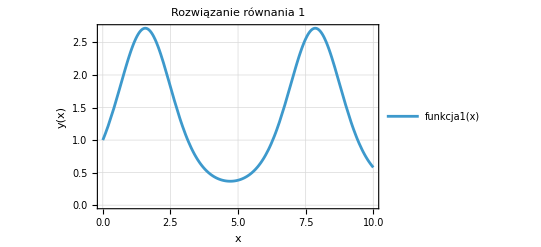

```mathematica
(*Wykres rozwiązania dla x od 0 do 10*)Plot[funkcja1[x],{x,0,10},PlotLabel->"Rozwiązanie równania 1",AxesLabel->{"x","y(x)"},PlotTheme->"Detailed"]
```

Zadanie 2.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja równania różniczkowego*)
rownanie2=y'[x]+2*y[x]==Sin[x];
```

```mathematica
(*Rozwiązanie symboliczne (użycie DSolve)*)
rozwiazanieDSolve2=DSolve[rownanie2,y[x],x]
(*Rozwiązanie zawiera stałą całkowania C[1],ponieważ nie podano warunku początkowego*)
```

{{y[x]→ⅇ^(-2 x) C[1]+1/5 (-Cos[x]+2 Sin[x])}}

```mathematica
(*Przykład:narysowanie rozwiązania dla warunku y(0)=0*)
warunekprzyklad2=y[0]==0;
rozwiazaniezWP2=DSolve[{rownanie2,warunekprzyklad2},y[x],x]
funkcja2[x_]=y[x]/. First[rozwiazaniezWP2]
```

{{y[x]→-1/5 ⅇ^(-2 x) (-1+ⅇ^(2 x) Cos[x]-2 ⅇ^(2 x) Sin[x])}}

-1/5 ⅇ^(-2 x) (-1+ⅇ^(2 x) Cos[x]-2 ⅇ^(2 x) Sin[x])

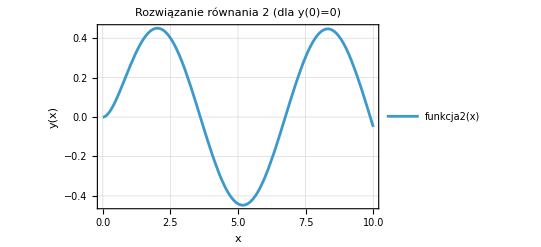

```mathematica
(*Wykres rozwiązania z przyjętym warunkiem początkowym y(0)=0 dla x od 0 do 10*)Plot[funkcja2[x],{x,0,10},PlotLabel->"Rozwiązanie równania 2 (dla y(0)=0)",AxesLabel->{"x","y(x)"},PlotTheme->"Detailed"]
```

Zadanie 3.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja równania różniczkowego*)
rownanie3=y'[x]+y[x]==y[x]^2;
```

```mathematica
(*Rozwiązanie z warunkiem początkowym y(0)=1/2*)warunekpoczatkowy3=y[0]==1/2;
rozwiazanieDSolve3=DSolve[{rownanie3,warunekpoczatkowy3},y[x],x]
funkcja3[x_]=y[x]/. First[rozwiazanieDSolve3]
```

{{y[x]→1/(1+ⅇ^x)}}

1/(1+ⅇ^x)

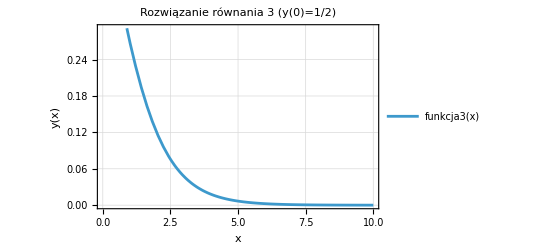

```mathematica
(*Wykres rozwiązania dla x od 0 do 10*)Plot[funkcja3[x],{x,0,10},PlotLabel->"Rozwiązanie równania 3 (y(0)=1/2)",AxesLabel->{"x","y(x)"},PlotTheme->"Detailed"]
```

Zadanie 4.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja równania różniczkowego*)
rownanie4=y''[x]+1/2*y'[x]+4*y[x]==0;
```

```mathematica
(*Przyjęcie warunków początkowych (brak w treści zadania):y(0)=1,y'(0)=0*)warunekpoczatkowy4a=y[0]==1;
warunekpoczatkowy4b=y'[0]==0;
```

```mathematica
(*Rozwiązanie symboliczne (użycie DSolve)*)rozwiazanieDSolve4=DSolve[{rownanie4,warunekpoczatkowy4a,warunekpoczatkowy4b},y[x],x]
funkcja4[x_]=y[x]/. First[rozwiazanieDSolve4]
```

{{y[x]→1/21 ⅇ^(-x/4) (21 Cos[(3 √7 x)/4]+√7 Sin[(3 √7 x)/4])}}

1/21 ⅇ^(-x/4) (21 Cos[(3 √7 x)/4]+√7 Sin[(3 √7 x)/4])

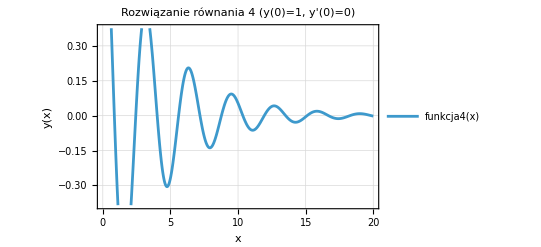

```mathematica
(*Wykres rozwiązania dla x od 0 do 20*)Plot[funkcja4[x],{x,0,20},PlotLabel->"Rozwiązanie równania 4 (y(0)=1, y'(0)=0)",AxesLabel->{"x","y(x)"},PlotTheme->"Detailed"]
```

Zadanie 5.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja parametru*)
omega=11/10;
```

```mathematica
(*Definicja równania różniczkowego i warunków początkowych*)rownanie5=y''[t]+y[t]==Cos[omega*t];
warunekpoczatkowy5a=y[0]==0;
warunekpoczatkowy5b=y'[0]==0;
```

```mathematica
(*Rozwiązanie symboliczne (użycie DSolve)*)rozwiazanieDSolve5=DSolve[{rownanie5,warunekpoczatkowy5a,warunekpoczatkowy5b},y[t],t]
funkcja5[t_]=y[t]/. First[rozwiazanieDSolve5]
```

{{y[t]→-5/21 (-20 Cos[t]+21 Cos[t/10] Cos[t]-Cos[t] Cos[(21 t)/10]-21 Sin[t/10] Sin[t]-Sin[t] Sin[(21 t)/10])}}

-5/21 (-20 Cos[t]+21 Cos[t/10] Cos[t]-Cos[t] Cos[(21 t)/10]-21 Sin[t/10] Sin[t]-Sin[t] Sin[(21 t)/10])

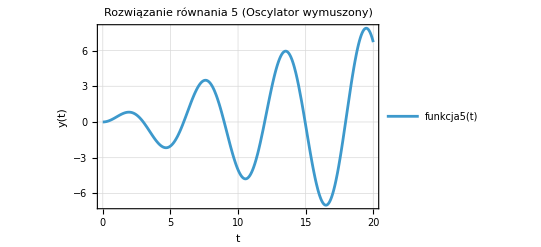

```mathematica
(*Wykres rozwiązania dla t od 0 do 20*)Plot[funkcja5[t],{t,0,20},PlotLabel->"Rozwiązanie równania 5 (Oscylator wymuszony)",AxesLabel->{"t","y(t)"},PlotTheme->"Detailed"]
```

Zadanie 6.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja parametrów*)r=1/2;
K=10;
y0=1;
```

```mathematica
(*Definicja równania różniczkowego i warunku początkowego*)rownanie6=y'[t]==r*y[t]*(1-y[t]/K);
warunekpoczatkowy6=y[0]==y0;
```

```mathematica
(*Rozwiązanie symboliczne (użycie DSolve)*)rozwiazanieDSolve6=DSolve[{rownanie6,warunekpoczatkowy6},y[t],t]
funkcja6[t_]=y[t]/. First[rozwiazanieDSolve6]
```

{{y[t]→(10 ⅇ^(t/2))/(9+ⅇ^(t/2))}}

(10 ⅇ^(t/2))/(9+ⅇ^(t/2))

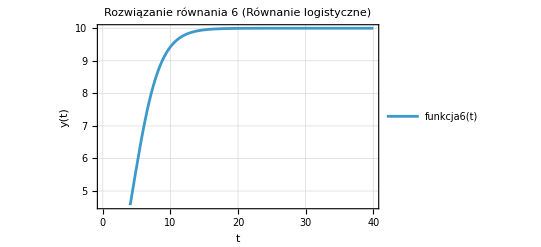

```mathematica
(*Wykres rozwiązania dla t od 0 do 40*)Plot[funkcja6[t],{t,0,40},PlotLabel->"Rozwiązanie równania 6 (Równanie logistyczne)",AxesLabel->{"t","y(t)"},PlotTheme->"Detailed"]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja parametrów*)delta=1/5;
alpha=-1;
beta=1.7;
gamma=3/10;
omega=6/5;
```

```mathematica
(*Definicja równania różniczkowego i warunków początkowych*)rownanie7=y''[t]+delta*y'[t]+alpha*y[t]+beta*y[t]^3==gamma*Cos[omega*t];
warunekpoczatkowy7a=y[0]==1/10;
warunekpoczatkowy7b=y'[0]==0;
```

```mathematica
(*Rozwiązanie numeryczne (użycie NDSolve)*)rozwiazanieNDSolve7=NDSolve[{rownanie7,warunekpoczatkowy7a,warunekpoczatkowy7b},y,{t,0,100}]
funkcja7[t_]=y[t]/. First[rozwiazanieNDSolve7]
```

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

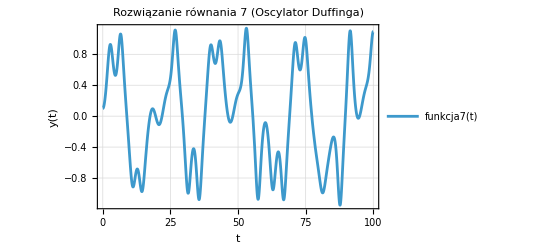

```mathematica
Plot[funkcja7[t],{t,0,100},PlotLabel->"Rozwiązanie równania 7 (Oscylator Duffinga)",AxesLabel->{"t","y(t)"},PlotTheme->"Detailed"]
```

Zadanie 8.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja parametrów*)alpha=1;
beta=0.1;
gamma=1.5;
delta=0.075;
```

```mathematica
(*Definicja układu równań i warunków początkowych*)uklad8={x'[t]==alpha*x[t]-beta*x[t]*y[t],y'[t]==-gamma*y[t]+delta*x[t]*y[t]};
warunkipoczatkowe8={x[0]==40,y[0]==9};
```

```mathematica
(*Rozwiązanie numeryczne (użycie NDSolve)*)rozwiazanieNDSolve8=NDSolve[{uklad8,warunkipoczatkowe8},{x,y},{t,0,50}]
funkcjakrok8[t_]=x[t]/. First[rozwiazanieNDSolve8]
funkcjapredator8[t_]=y[t]/. First[rozwiazanieNDSolve8]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
(*Wykres rozwiązania dla x(t) (ofiara) i y(t) (drapieżnik) dla t od 0 do 50*)Plot[{funkcjakrok8[t],funkcjapredator8[t]},{t,0,50},PlotLabels->{"Ofiara x(t)","Drapieżnik y(t)"},PlotLabel->"Rozwiązanie układu Lotki-Volterry",AxesLabel->{"t","Populacja"},PlotTheme->"Detailed"]
```

-Graphics-

Zadanie 9.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja równania różniczkowego i warunków brzegowych*)rownanie9=y''[x]+Pi^2*y[x]==Sin[2*x];
warunkibrzegowe9={y[0]==0,y[1]==0};
```

```mathematica
(*Rozwiązanie numeryczne (użycie NDSolve-NDSolve może rozwiązywać zadania brzegowe)*)rozwiazanieNDSolve9=NDSolve[{rownanie9,warunkibrzegowe9},y,{x,0,1}]
funkcja9[x_]=y[x]/. First[rozwiazanieNDSolve9]
```

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…][x]

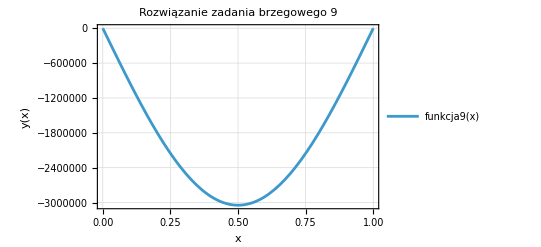

```mathematica
(*Wykres rozwiązania dla x od 0 do 1*)Plot[funkcja9[x],{x,0,1},PlotLabel->"Rozwiązanie zadania brzegowego 9",AxesLabel->{"x","y(x)"},PlotTheme->"Detailed"]
```

Zadanie 10.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Definicja parametru*)
mu=1000;
```

```mathematica
(*Definicja równania różniczkowego i warunków początkowych*)rownanie10=y''[t]-mu*(1-y[t]^2)*y'[t]+y[t]==0;
warunekpoczatkowy10a=y[0]==2;
warunekpoczatkowy10b=y'[0]==0;
```

```mathematica
(*Rozwiązanie numeryczne (użycie NDSolve)*)
rozwiazanieNDSolve10=NDSolve[{rownanie10,warunekpoczatkowy10a,warunekpoczatkowy10b},y,{t,0,300}]
funkcja10[t_]=y[t]/. First[rozwiazanieNDSolve10]
```

{{y→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

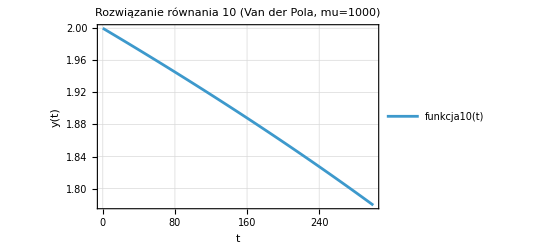

```mathematica
(*Wykres rozwiązania dla t od 0 do 300*)Plot[funkcja10[t],{t,0,300},PlotLabel->"Rozwiązanie równania 10 (Van der Pola, mu=1000)",AxesLabel->{"t","y(t)"},PlotTheme->"Detailed"]
```